### Derivatives and nested functions

```mathematica
f[x_]:= r x (1-x)
```

```mathematica
D[f[x],x]
```

r (1-x)-r x

#### Fixed point and the first bifurcation point

```mathematica
fp1 = Solve[f[x]==x,x]
```

{{x→0},{x→(-1+r)/r}}

```mathematica
fp1[[2,1]]
```

x→(-1+r)/r

```mathematica
eq1 = D[f[x],x] /. fp1[[2,1]]
```

1-r+(1-(-1+r)/r) r

```mathematica
eq1 /. r->1
```

1

```mathematica
eq1==1
```

1-r+(1-(-1+r)/r) r==1

```mathematica
Solve[eq1==-1,r]
```

{{r→3}}

#### Nested function

```mathematica
f[f[x]]
```

r^2 (1-x) x (1-r (1-x) x)

```mathematica
D[f[f[x]],x]
```

r^2 (1-x) x (-r (1-x)+r x)+r^2 (1-x) (1-r (1-x) x)-r^2 x (1-r (1-x) x)

### Creating the trajectory in the (x_t, x_t+1) plane

```mathematica
a1= NestList[Evaluate[f[#] /. r->3.9]&,0.1,10]
```

{0.1,0.351,0.888416,0.386618,0.924864,0.271013,0.770504,0.689628,0.83476,0.537949,0.969384}

```mathematica
a1
```

{0.1,0.351,0.888416,0.386618,0.924864,0.271013,0.770504,0.689628,0.83476,0.537949,0.969384}

```mathematica
Partition[a1,2,1]
```

{{0.1,0.351},{0.351,0.888416},{0.888416,0.386618},{0.386618,0.924864},{0.924864,0.271013},{0.271013,0.770504},{0.770504,0.689628},{0.689628,0.83476},{0.83476,0.537949},{0.537949,0.969384}}

```mathematica
a1 /. x_Real ->  {x,x}
```

{{0.1,0.1},{0.351,0.351},{0.888416,0.888416},{0.386618,0.386618},{0.924864,0.924864},{0.271013,0.271013},{0.770504,0.770504},{0.689628,0.689628},{0.83476,0.83476},{0.537949,0.537949},{0.969384,0.969384}}

```mathematica
Length[Partition[a1,2,1]]
```

10

```mathematica
Length[a1 /. x_Real -> {x,x}]
```

11

```mathematica
Prepend[Partition[a1,2,1],{a1[[1]],0}]
```

{{0.1,0},{0.1,0.351},{0.351,0.888416},{0.888416,0.386618},{0.386618,0.924864},{0.924864,0.271013},{0.271013,0.770504},{0.770504,0.689628},{0.689628,0.83476},{0.83476,0.537949},{0.537949,0.969384}}

```mathematica
Thread[{Prepend[Partition[a1,2,1],{a1[[1]],0}],a1 /. x_Real -> {x,x}}]
```

{{{0.1,0},{0.1,0.1}},{{0.1,0.351},{0.351,0.351}},{{0.351,0.888416},{0.888416,0.888416}},{{0.888416,0.386618},{0.386618,0.386618}},{{0.386618,0.924864},{0.924864,0.924864}},{{0.924864,0.271013},{0.271013,0.271013}},{{0.271013,0.770504},{0.770504,0.770504}},{{0.770504,0.689628},{0.689628,0.689628}},{{0.689628,0.83476},{0.83476,0.83476}},{{0.83476,0.537949},{0.537949,0.537949}},{{0.537949,0.969384},{0.969384,0.969384}}}

```mathematica
Flatten[Thread[{Prepend[Partition[a1,2,1],{a1[[1]],0}],a1 /. x_Real -> {x,x}}],1]
```

{{0.1,0},{0.1,0.1},{0.1,0.351},{0.351,0.351},{0.351,0.888416},{0.888416,0.888416},{0.888416,0.386618},{0.386618,0.386618},{0.386618,0.924864},{0.924864,0.924864},{0.924864,0.271013},{0.271013,0.271013},{0.271013,0.770504},{0.770504,0.770504},{0.770504,0.689628},{0.689628,0.689628},{0.689628,0.83476},{0.83476,0.83476},{0.83476,0.537949},{0.537949,0.537949},{0.537949,0.969384},{0.969384,0.969384}}

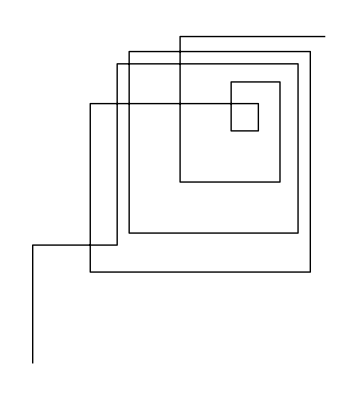

```mathematica
Graphics[Line[Flatten[Thread[{Prepend[Partition[a1,2,1],{a1[[1]],0}],a1 /. x_Real -> {x,x}}],1]]]
```

```mathematica
createSpiderWeb[list_]:=Graphics[Line[Flatten[Thread[{Prepend[Partition[list,2,1],{list[[1]],0}],list /. x_Real -> {x,x}}],1]]]
```

```mathematica
a2= NestList[Evaluate[f[#] /. r->3.7]&,0.1,1000];
```

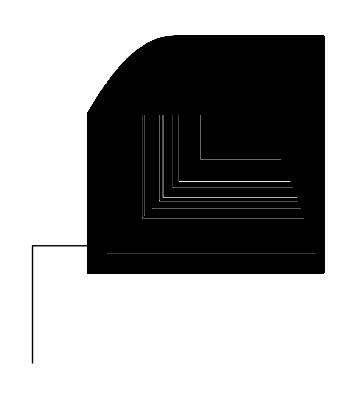

```mathematica
createSpiderWeb[a2]
```